Autor: Dawid Bitner

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 5

Metoda kolejnych przybliżeń

## Równanie Fredholma II rodzaju

### Zadanie 1

Wyznaczyć metodą kolejnych przybliżeń rozwiązanie przybliżone y_n równania

y(x)=ⅇ^x-1/4∫_0^1 (x ⅇ^t y(t))ⅆt

Argument:  n

Sprawdzić, czy metodę można zastosować. 
Wyznaczyć rozwiązanie dla kilku wartości n. 
Na tej podstawie odgadnąć rozwiązanie dokładne i sprawdzić jego poprawność.

### Zadanie 2

Wyznaczyć rozwiązania przybliżone y_n dla  n=2,4,6,8, równania:

y(x)=sin x + (x-1)/4+1/4∫_0^(π/2) (t-x)  y(t)ⅆt.

Utworzyć wykresy porównujące rozwiązanie przybliżone z rozwiązaniem dokładnym, którym jest funkcja y(x)=sin x, np.  w postaci:

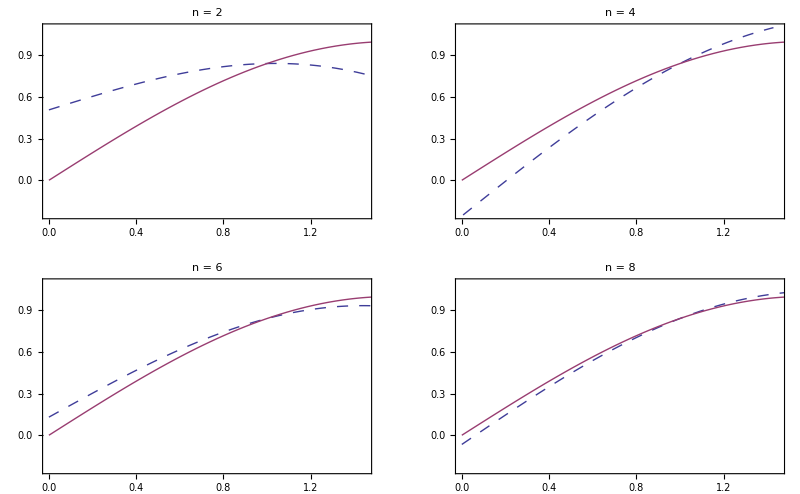

```mathematica
(*zad1*)
kp[f_, a_, b_, k_, λ_, n_]:=Module[{y,M,req,res,result,lastRes,newRes,int},
M = MaxValue[{k[x,t], a≤ x≤b, a≤t≤b}, {x,t}];
req = Abs[λ ]≥1/(M(b-a));
If[req, Return["Nie spełnia warunku zbieżności"]];
res ={f[x]};
Do[
lastRes = Last[res];
newRes = Integrate[k[x,t]*(lastRes/.{x->t}),{t, a,b}];
AppendTo[res, newRes];
,{i,1,n+1}];
result = Sum[λ^i*res⟦i+1⟧, {i, 0, n}];
Return[Simplify[result]];
];
```

```mathematica
fun[x_]:=Exp[x]-1/4∫_0^1 (x*Exp[t]*y[t])ⅆt;
k[x_,t_]:=x*Exp[t];
f[x_]:=Exp[x];
λ=-1/4;
a = 0;
b = 1;
Do[
r = kp[f,a,b,k,λ,i];
Print["Wynik dla n = ", i, " : ", r ];
,{i, 2,6}];
```

Wynik dla n = 2 : ⅇ^x-3/32 (-1+ⅇ^2) x

Wynik dla n = 3 : ⅇ^x-13/128 (-1+ⅇ^2) x

Wynik dla n = 4 : ⅇ^x-51/512 (-1+ⅇ^2) x

Wynik dla n = 5 : ⅇ^x-(205 (-1+ⅇ^2) x)/2048

Wynik dla n = 6 : ⅇ^x-(819 (-1+ⅇ^2) x)/8192

Rozwiązanie: 1/10 (10 ⅇ^x+x-ⅇ^2 x)

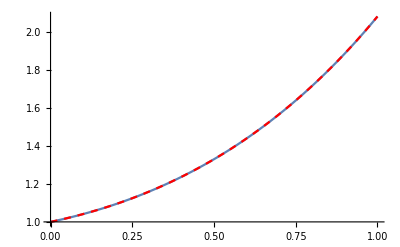

```mathematica
(* Rozwiązanie *)
solve = DSolveValue[y[x]==Exp[x]-1/4∫_0^1 (x*Exp[t]*y[t])ⅆt, y[x],x];
Print["Rozwiązanie: ", solve];
rPlot = Plot[r, {x, a,b}, PlotRange->All, PlotStyle->{Dashed, Red}];
sPlot = Plot[solve, {x,a,b}, PlotRange->All];
Show[sPlot, rPlot]
```

Dla n = 2 : (π^4-π^4 x+12288 Sin[x])/12288

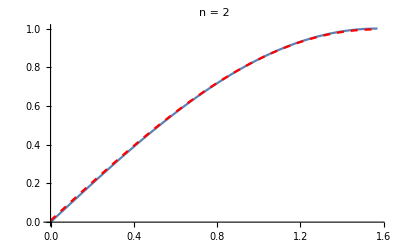

Dla n = 4 : (π^8 (-1+x))/37748736+Sin[x]

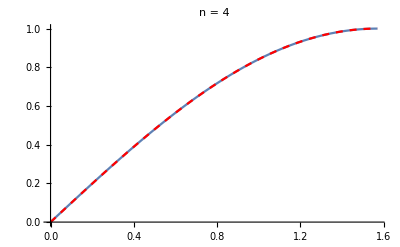

Dla n = 6 : -(π^12 (-1+x))/115964116992+Sin[x]

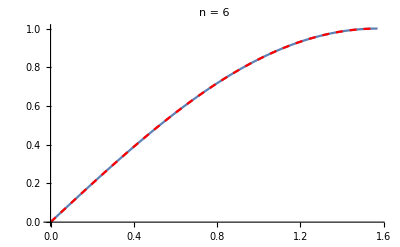

Dla n = 8 : (π^16 (-1+x))/356241767399424+Sin[x]

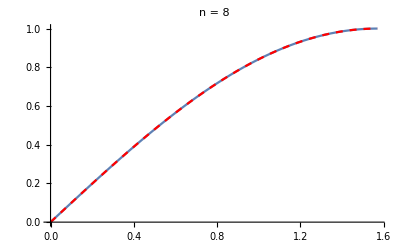

```mathematica
(*zad2*)
fun2[x_]:= Sin[x]+(x-1)/4+1/4∫_0^(π/2) (t-x)y[t]ⅆt;
k2[x_,t_]:=t-x;
f2[x_]:=Sin[x]+(x-1)/4;
λ2=1/4;
a2=0;
b2=π/2;
sin = Plot[Sin[x], {x,a2,b2}, PlotRange->All];

Do[
r = kp[f2,a2,b2,k2,λ2,i];
p = Plot[r, {x,a2,b2}, PlotRange->All, PlotStyle->{Dashed, Red}];
Print["Dla n = ", i , " : ", r ];
Print[Show[sin,p, PlotLabel->StringForm["n = `1`", i]]];
,{i, 2,8,2}];
```